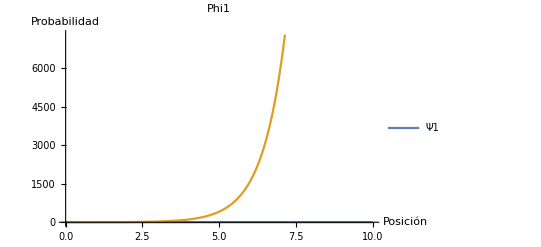

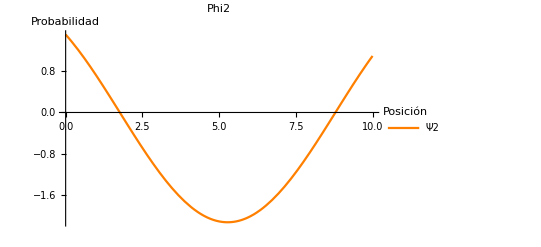

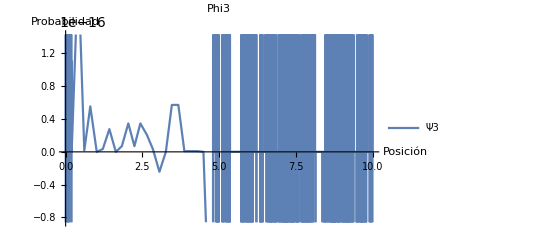

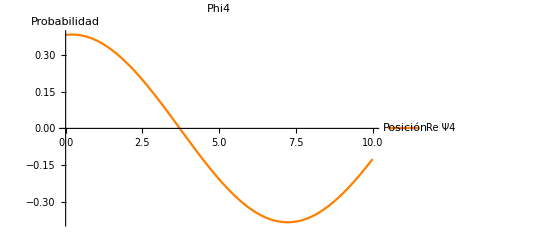

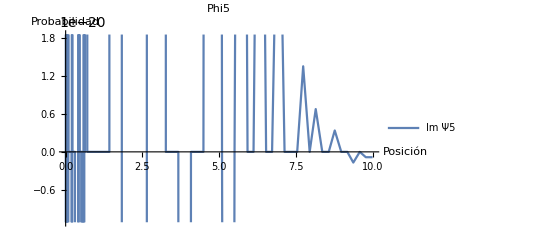

```mathematica
Clear["Global`"]
ko=I*Sqrt[2*m*(9*V/10)]/ℏ;
k1=Sqrt[2*m*(1*V/10)]/ℏ;

eq1[x_]:=Exp[ko*I*x]+B*Exp[-ko*I*x]
eq2[x_]:=A*Exp[k1*I*x]+U*Exp[-k1*I*x]
eq3[x_]:=P*Exp[ko*I*x]+F*Exp[-ko*I*x]
eq4[x_]:=G*Exp[k1*I*x]+J*Exp[-k1*I*x]
eq5[x_]:=H*Exp[ko*I*x]

n1=eq1[0];
n2=eq2[0];
n3=eq2[a];
n4=eq3[a];
n5=eq3[2a];
n6=eq4[2a];
n7=eq4[3a];
n8=eq5[3a];

m1=D[eq1[x],x]/.x->0;
m2=D[eq2[x],x]/. x->0;
m3=D[eq2[x],x]/. x->a;
m4=D[eq3[x],x]/. x->a;
m5=D[eq3[x],x]/. x->2a;
m6=D[eq4[x],x]/. x->2a;
m7=D[eq4[x],x]/. x->3a;
m8=D[eq5[x],x]/. x->3a;

coef=Solve[{n1==n2,n3==n4,n5==n6,n7==n8,m1==m2,m3==m4,m5==m6,m7==m8},{A,U,F,H,B,P,G,J}];

m=1;
ℏ=1;
a=1;
V=1;
ψ1[x_]:=eq1[x]/.coef[[1,5]]
ψ2[x_]:=eq2[x]/.coef[[1,1]]/.coef[[1,2]]
ψ3[x_]:=eq3[x]/.coef[[1,3]]/.coef[[1,6]]
ψ4[x_]:=eq4[x]/.coef[[1,7]]/.coef[[1,8]]
ψ5[x_]:=eq5[x]/.coef[[1,4]]
(*
V=2;
ψ12[x_]:=eq1[x]/.coef[[1,5]]
ψ22[x_]:=eq2[x]/.coef[[1,1]]/.coef[[1,2]]
ψ32[x_]:=eq3[x]/.coef[[1,3]]/.coef[[1,6]]
ψ42[x_]:=eq4[x]/.coef[[1,7]]/.coef[[1,8]]
ψ52[x_]:=eq5[x]/.coef[[1,4]]
*)
(*FullSimplify[ψ11[x]];
FullSimplify[ψ21[x]];
FullSimplify[ψ31[x]];
FullSimplify[ψ41[x]];
FullSimplify[ψ51[x]];*)
Plot[{Im[ψ1[x]],Re[ψ1[x]]},{x,0,10},PlotLegends->{"Ψ1"},PlotLabel->"Phi1",AxesLabel->{"Posición","Probabilidad"}]
Plot[{Re[ψ2[x]]},{x,0,10},PlotLegends->{"Ψ2"},PlotLabel->"Phi2",AxesLabel->{"Posición","Probabilidad"},PlotStyle->Orange]
Plot[{Im[ψ3[x]]},{x,0,10},PlotLegends->{" Ψ3"},PlotLabel->"Phi3",AxesLabel->{"Posición","Probabilidad"}]
Plot[{Re[ψ4[x]]},{x,0,10},PlotLegends->{"Re Ψ4"},PlotLabel->"Phi4",AxesLabel->{"Posición","Probabilidad"},PlotStyle->Orange]
Plot[{Im[ψ5[x]]},{x,0,10},PlotLegends->{"Im Ψ5"},PlotLabel->"Phi5",AxesLabel->{"Posición","Probabilidad"}]
```